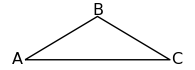

```mathematica
Graphics[{Line[{{-1,0},{0,.7},{1,0},{-1,0}}],Text[Style["A",16],{-1.1,0}], Text[Style["B",16],{0,.8}], Text[Style["C",16],{1.1,0}
], ImageSize->80}]
```

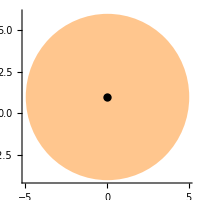

```mathematica
Graphics[{Lighter[Lighter[Orange]],Disk[{0,1},5],Black,PointSize[0.03],Point[{0,1}]},Axes->True,ImageSize->200]
```

```mathematica
Solve[x^2+(y-1)^2==5^2,{y}]
```

{{y→1-√(25-x^2)},{y→1+√(25-x^2)}}

```mathematica
lc[x_]:=1-Sqrt[25-x^2]
```

```mathematica
uc[x_]:=1+Sqrt[25-x^2]
```

```mathematica
{lc[x],uc[x]}
```

{1-√(25-x^2),1+√(25-x^2)}

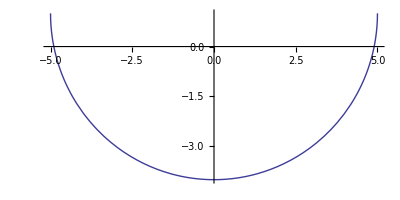

```mathematica
Plot[lc[x],{x,-5,5},AxesOrigin->{0,0},AspectRatio->1/2]
```

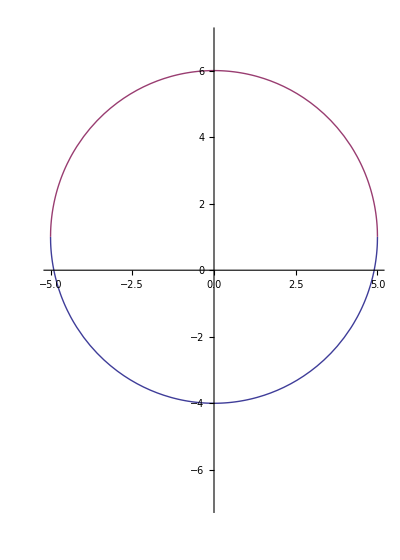

```mathematica
Plot[{lc[x],uc[x]},{x,-5,5},PlotRange->7,AxesOrigin->{0,0},AspectRatio->7/5]
```